```mathematica
CalibrationHg=Import["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Phys_Labs\\5_sem\\Exam lab\\Calibration_Hg.xlsx"][[1]][[2;;All,1;;2]];
```

```mathematica
calibWaveLengths=CalibrationHg[[All,1]];
calibPixel=CalibrationHg[[All,2]];
calibrationHgReady=Transpose[ArrayReshape[AppendTo[calibPixel,calibWaveLengths],{2,Length[calibWaveLengths]}]];
```

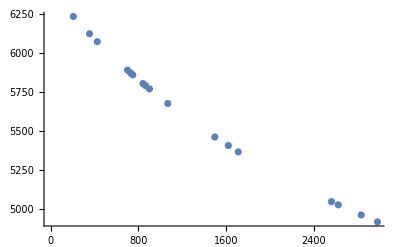

```mathematica
ListPlot[calibrationHgReady]
```

```mathematica
fit=FindFit[calibrationHgReady,{a+c/(x-b),b<0},{a,b,c},x]
```

{a→2889.97,b→-4060.89,c→1.42866×10^7}

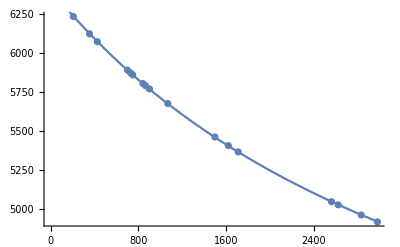

```mathematica
Show[ListPlot[calibrationHgReady],Plot[a+c/(x-b)/.fit,{x,0,3000}]]
```

```mathematica
lampSpectre=ReadList["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Phys_Labs\\5_sem\\Exam lab\\26_11_2018\\lamp2.txt",Number,WordSeparators->{"\t", "\n"}];
```

```mathematica
lampSpectre=ArrayReshape[lampSpectre,{Length[lampSpectre]/5,5}];
```

```mathematica
i2Spectre=ReadList["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Phys_Labs\\5_sem\\Exam lab\\26_11_2018\\i2-clear.txt",Number,WordSeparators->{"\t", "\n"}];
```

```mathematica
i2Spectre=ArrayReshape[i2Spectre,{Length[i2Spectre]/5,5}];
```

```mathematica
len=Length[lampSpectre]
```

30071

```mathematica
peaks={};
```

```mathematica
Manipulate[Grid[{{p+x},{ListLinePlot[i2Spectre[[x;;y,Channel+1]],ImageSize->Large]},peaks}],{{x,0,"Begin"},1,len},{{y,Length[lampSpectre],"End"},1,len},{Channel,{1,2,3,4}},
Button["Add",AppendTo[peaks,MinimalBy[Transpose[{i2Spectre[[x+p[[1]]-50;;x+p[[1]]+50,1]],i2Spectre[[x+p[[1]]-50;;x+p[[1]]+50,Channel+1]]}],Last][[1]]]],
Button["Clear",peaks={}],
{{p,{0,0}},Locator},
ContentSize->{600, 460}
]
```

```mathematica
peaks
```

{{956.7,1395.07},{1015.1,1325.96},{1073.1,1236.08},{1130.7,1187.76},{1187.4,1120.29},{1241.8,1056.73},{1299.5,987.456},{1330.,993.664}}

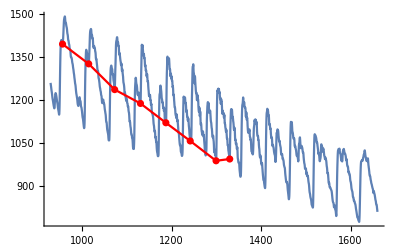

```mathematica
Show[ListLinePlot[Transpose[{i2Spectre[[9300.;;16600.,1]],i2Spectre[[9300;;16600.,3]]}]],ListPlot[peaks,PlotStyle->Red],ListLinePlot[peaks,PlotStyle->Red]]
```

```mathematica
peaksStorage={};
AppendTo[peaksStorage,Transpose[peaks]]
```

{{{952.3,1015.1,1073.1,1130.7},{1377.92,1325.96,1236.08,1187.76}}}

```mathematica
AppendTo[peaksStorage,Transpose[peaks]]
```

{{{952.3,1015.1,1073.1,1130.7},{1377.92,1325.96,1236.08,1187.76}},{{952.3,1015.1,1073.1,1130.7},{1377.92,1325.96,1236.08,1187.76}}}